```mathematica
PrintGraph[mat_,z_]:=Module[{},
Print[z," ",Length@WeaklyConnectedComponents@AdjacencyGraph@mat];
Print[AdjacencyGraph[mat,VertexLabels->Automatic]]
](*функция вывода графа, получает матрицу инцедентности и выводит еще номер этого графа (сделал для удобства подсчета) и число компонент*)
```

```mathematica
f[len_, max_]:=Module[{list, newlist={},i,k},
If[len≠1,list = f[len-1, max ],Return[Table[{k},{k,1,max}]]];
For[i=1,i≤max,i++,
newlist=Join[newlist,Map[Append[#,i]&,list]]
];
Return@newlist
](*функция выдающая списое отображений (всех)*)
```

```mathematica
getfuncMat[func_]:=Module[{mat=Table[Table[0,Length@func],Length@func]},
For[i=1,i≤Length@func,i++,mat[[i,func[[i]]]]=1];
mat](*функция получения матрицы отображения*)
```

```mathematica
n=6;(*можность алфавита*)
ls = f[n,n];
ls=getfuncMat/@ls;(*тут получаю матрицу отображения*)
```

```mathematica
MatrixForm/@ls
```

{(1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),46505,(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1)}
 |  |  |  |

```mathematica
WeaklyConnectedComponents@AdjacencyGraph@{{1,0,0},{1,0,0},{1,0,0}}(*так работает функция вывода всех компонент (можно узнать его длину это и будет число компонент)*)
```

{{1,2,3}}

```mathematica
sum=0;
For[i=1,i≤ Length@ls,i++,If[Length@WeaklyConnectedComponents@AdjacencyGraph@(ls[[i]])==2,sum+=Length@WeaklyConnectedComponents@AdjacencyGraph@MatrixPower[ls[[i]],3]]]
Print[sum](*это тут я для себя счичтал сколько у меня будут давать компонент отображения, которые изначально(без возведения в степень) имели 2 компоненты*)
```

44508

1 2

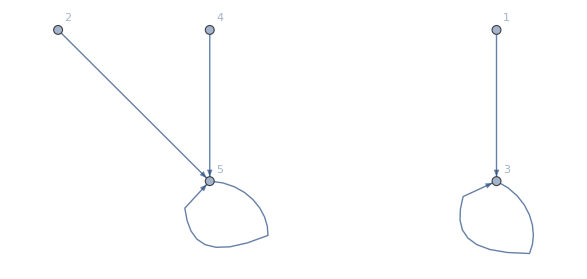

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
PrintGraph[({{0, 0, 1, 0, 0}, {0, 0, 0, 0, 1}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 1}, {0, 0, 0, 0, 1}}),1]
```

1 1

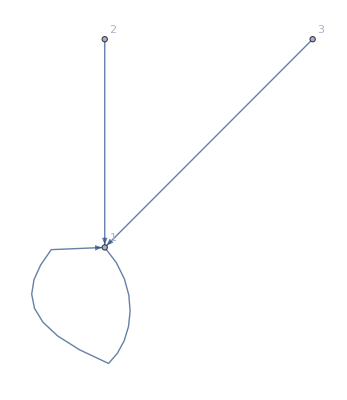

2 1

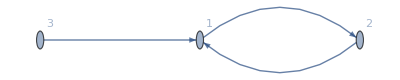

3 1

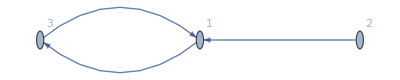

4 2

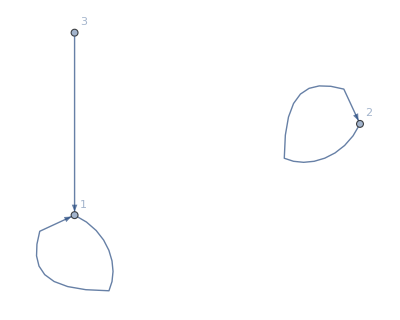

5 1

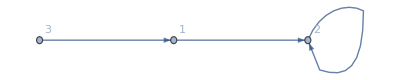

6 2

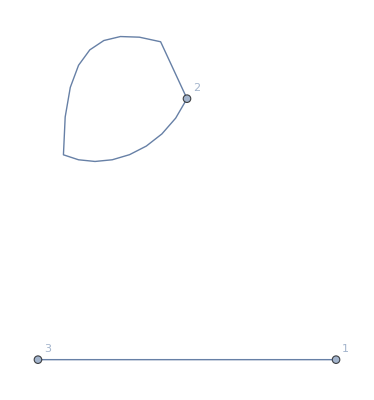

7 1

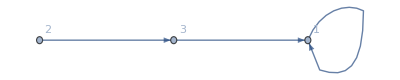

8 1

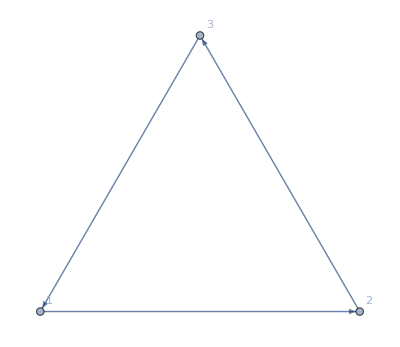

9 1

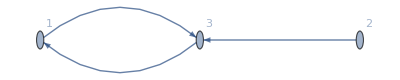

10 1

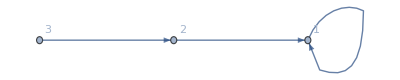

11 1

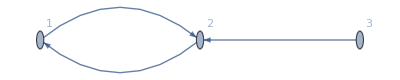

12 1

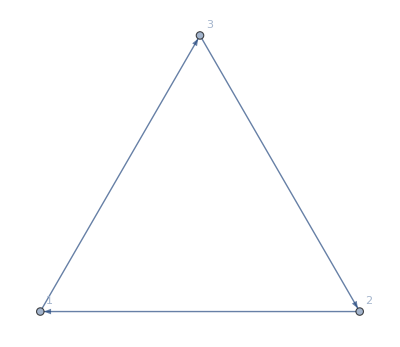

13 2

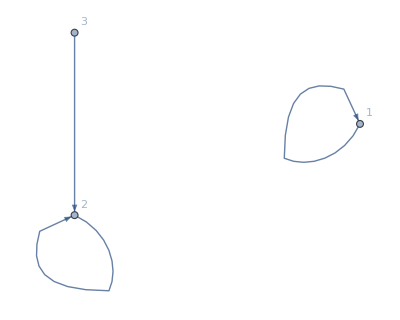

14 1

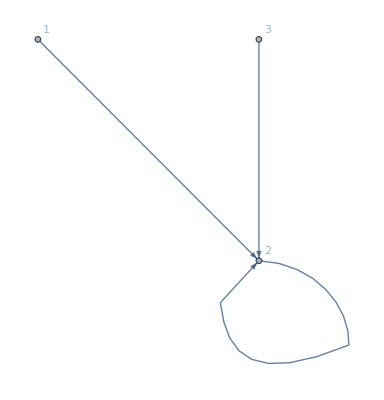

15 1

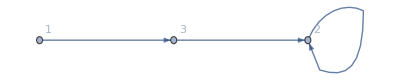

16 2

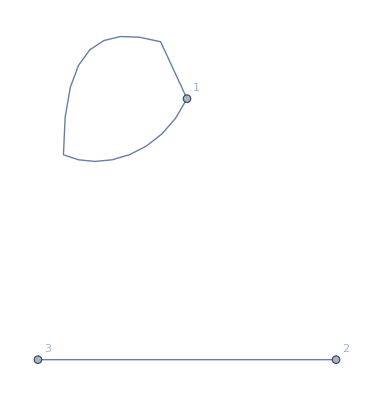

17 1

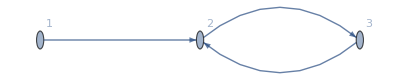

18 1

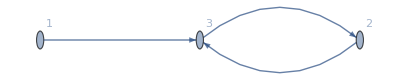

19 2

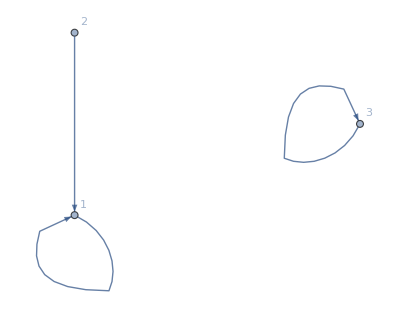

20 2

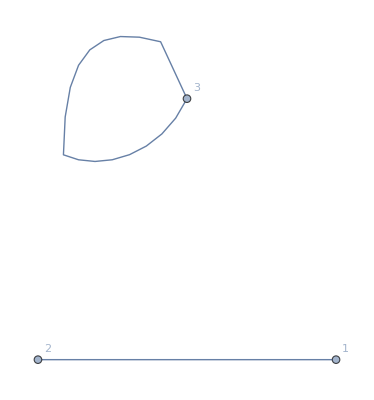

21 1

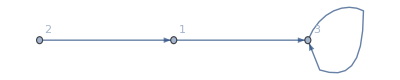

22 3

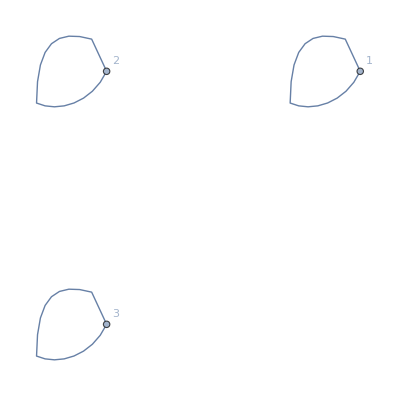

23 2

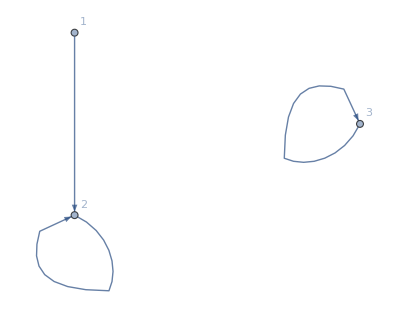

24 2

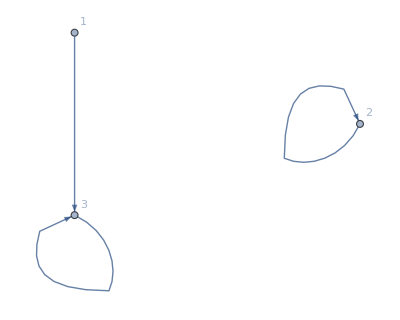

25 2

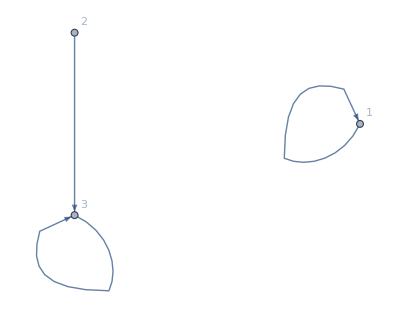

26 1

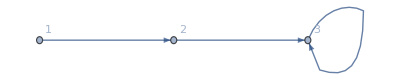

27 1

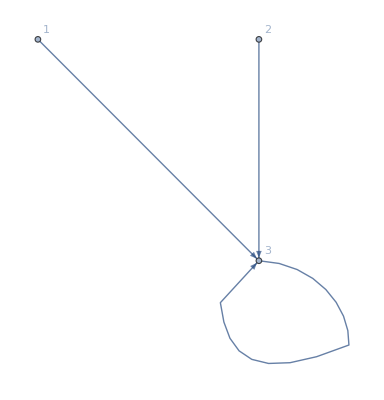

```mathematica
For[i=1,i≤Length@ls,i++,PrintGraph[ls[[i]],i]](*тут можно узнать все отображения и как они выглядят*)
```

```mathematica
sum=0;
For[i=1,i≤Length@ls,i++,sum+=Length@WeaklyConnectedComponents@AdjacencyGraph@(MatrixPower[ls[[i]],2])]
Print[sum](*тут считаю в лоб, сколько у меня будет компонент образовываться суммарно при возведении всех отображений в квадрат*)
```

47